```mathematica
SetDirectory[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"out", "schaeferTurek"}]]
```

/home/florian/Projects/university/masters_thesis/code/2D/out/schaeferTurek

```mathematica
srts = Complement[FileNames[], FileNames["*time"], FileNames["cumulant*"]];
cumulants = Complement[FileNames[], FileNames["*time"], FileNames["srt*"]];
```

```mathematica
values = {2,3,4,5,7,10,15,20,25,30,40};
```

```mathematica
loadCSV[collision_String,size_Integer]:=Delete[Import[collision<>"_Re100_size"<>ToString[size],"CSV"],1];
loadDragData[collision_String,size_Integer] := Drop[Map[Delete[#,3]&,loadCSV[collision,size]],1000];loadLiftData[collision_String,size_Integer] := Drop[Map[Delete[#,2]&,loadCSV[collision,size]],1000];

dragDataFrequency[collision_String, size_Integer] := Abs[Fourier[ #[[2]]&/@dragData[collision,size]]];
liftDataFrequency[collision_String, size_Integer] := Abs[Fourier[ #[[2]]&/@liftData[collision,size]]];

maximaPositions[list_] :=1+Position[Differences[Sign[Differences[list[[All,2]]]]],-2];
minimaPositions[list_] :=1+Position[Differences[Sign[Differences[list[[All,2]]]]],2]

lastWavelimits[data_]:=Flatten[ Take[maximaPositions[data],-2]];
lastWavelength[data_]:=Differences[lastWavelimitsLift[data]][[1]];

lastWaveLift[data_]  := Take[data,lastWavelimitsLift[data]];


getCumulantAndSRT[size_Integer] :={getDragData["cumulant",size],getDragData["srt", size]};

PlotCumulantVsSRT[size_Integer] := ListLinePlot[getCumulantAndSRT[size],PlotLegends->{"cumulant","SRT"}];
getCumulantAndNextSRT[position_Integer] := {getDragData["cumulant",values[[position]]],getDragData["srt", values[[position+1]]]};
PlotCumulantVsNextSRT[position_Integer] := ListLinePlot[getCumulantAndNextSRT[position],PlotLegends->{"cumulant","SRT"}];
getCumulantAndShiftSRT[position_Integer,shift_Integer] := {getDragData["cumulant",values[[position]]],getDragData["srt", values[[position+shift]]]};
PlotCumulantVsShiftSRT[position_Integer,shift_Integer] := ListLinePlot[getCumulantAndShiftSRT[position,shift],PlotLegends->{"cumulant","SRT"}];
getCumulantsFromTo[start_Integer,end_Integer] := getDragData["cumulant",values[[#]]]&/@Range[start,end];
plotCumulantsFromTo[start_Integer,end_Integer] := ListLinePlot[getCumulantsFromTo[start,end],PlotLegends->ToString /@ (values[[#]]&/@ Range[3,8])];getSRTFromTo[start_Integer,end_Integer] := getDragData["srt",values[[#]]]&/@Range[start,end];
plotSRTFromTo[start_Integer,end_Integer] := ListLinePlot[getSRTFromTo[start,end],PlotLegends->ToString /@ (values[[#]]&/@ Range[3,8])];
getCumulantsFrequencyFromTo[start_Integer,end_Integer] := getDragDataFrequency["cumulant",values[[#]]]&/@Range[start,end];
plotCumulantsFrequencyFromTo[start_Integer,end_Integer] := ListLinePlot[getCumulantsFrequencyFromTo[start,end],PlotLegends->ToString /@ (values[[#]]&/@ Range[3,8]), PlotRange->All];plotCumulantsFrequencyFromToClip[start_Integer,end_Integer,clip_Integer] := ListLinePlot[Take[#,clip]&/@getCumulantsFrequencyFromTo[start,end],PlotLegends->ToString /@ (values[[#]]&/@ Range[3,8]), PlotRange->All];getSRTFrequencyFromTo[start_Integer,end_Integer] := getDragDataFrequency["srt",values[[#]]]&/@Range[start,end];
plotSRTFrequencyFromTo[start_Integer,end_Integer] := ListLinePlot[getSRTFrequencyFromTo[start,end],PlotLegends->ToString /@ (values[[#]]&/@ Range[3,8]), PlotRange->All];
plotSRTFrequencyFromToClip[start_Integer,end_Integer,clip_Integer] := ListLinePlot[Take[#,clip]&/@getSRTFrequencyFromTo[start,end],PlotLegends->ToString /@ (values[[#]]&/@ Range[3,8]), PlotRange->All];
```

```mathematica
getLastWaveLift["cumulant",15]
getLastWavelengthLift["cumulant",15]
```

{1751,1873}

122

```mathematica
plotCumulantsFromTo[4,9]
```

Drop::drop: Cannot drop positions 1 through 1000 in {}.

ListLinePlot::lpn: {«1»} is not a list of numbers or pairs of numbers.

ListLinePlot[{1},PlotLegends→{4,5,7,10,15,20}]
 |  |  |  |

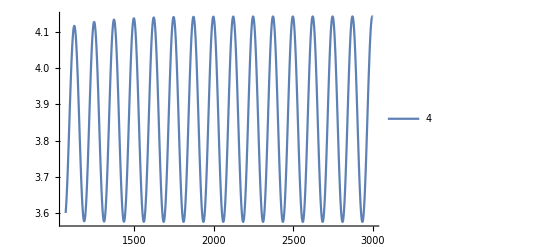

```mathematica
plotSRTFromTo[10,10]
```

Drop::drop: Cannot drop positions 1 through 1000 in {}.

Part::partw: Part 2 of {} does not exist.

Part::partd: Part specification 1000⟦2⟧ is longer than depth of object.

Drop::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Drop[{}⟦2⟧,1000⟦2⟧].

Fourier::fftl: Argument Drop[{}⟦2⟧,1000⟦2⟧] is not a non-empty list or rectangular array of numeric quantities.

Take::take: Cannot take positions 1 through 3 in Abs[Fourier[Drop[{}⟦2⟧,1000⟦2⟧]]].

ListLinePlot::lpn: {{87.6499,0.127166,0.0697964},{166.788,0.0307854,0.0330509},{126.779,0.0856378,0.0871544},{128.552,0.0179646,0.0210698},Take[Abs[Fourier[Drop[{}⟦2⟧,1000⟦2⟧]]],3],{148.955,0.0331133,0.0472423},{151.164,0.320411,0.262489}} is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

ListLinePlot[{{87.6499,0.127166,0.0697964},{166.788,0.0307854,0.0330509},{126.779,0.0856378,0.0871544},{128.552,0.0179646,0.0210698},Take[Abs[Fourier[Drop[{}⟦2⟧,1000⟦2⟧]]],3],{148.955,0.0331133,0.0472423},{151.164,0.320411,0.262489}},PlotLegends→{4,5,7,10,15,20},PlotRange→All]

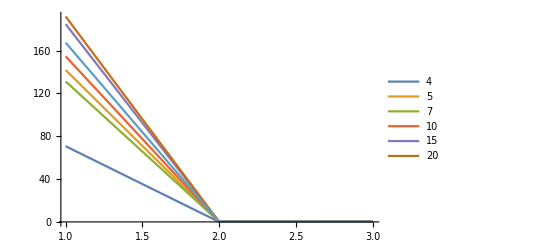

```mathematica
plotCumulantsFrequencyFromToClip[2,8,3]
plotSRTFrequencyFromToClip[2,8,3]
```

```mathematica
points = getLiftData["cumulant", 10];

maxima=1+Position[Differences[Sign[Differences[points[[All,2]]]]],-2]
minima=1+Position[Differences[Sign[Differences[points[[All,2]]]]],2]

peaks=Extract[points,maxima]
ListLinePlot[points,Prolog->{PointSize[Large],Red,Point[Extract[points,maxima]],Green,Point[Extract[points,minima]]}]
```

Drop::drop: Cannot drop positions 1 through 1000 in {}.

Part::partw: Part 2 of {} does not exist.

Differences::listrp: List or SparseArray or StructuredArray expected at position 1 in Differences[Drop[{},1000]⟦All,2⟧].

Differences::listrp: List or SparseArray or StructuredArray expected at position 1 in Differences[Sign[Differences[Drop[{},1000]⟦All,2⟧]]].

{}

Part::partw: Part 2 of {} does not exist.

Differences::listrp: List or SparseArray or StructuredArray expected at position 1 in Differences[Drop[{},1000]⟦All,2⟧].

Differences::listrp: List or SparseArray or StructuredArray expected at position 1 in Differences[Sign[Differences[Drop[{},1000]⟦All,2⟧]]].

{{2,2,2,4}}

{}

Extract::partd: Part specification {2,2,2,4} is longer than depth of object.

ListLinePlot::lpn: Drop[{},1000] is not a list of numbers or pairs of numbers.

ListLinePlot[Drop[{},1000],Prolog→{PointSize[Large],RGBColor[1, 0, 0],Point[{}],RGBColor[0, 1, 0],Point[Extract[Drop[{},1000],{{2,2,2,4}}]]}]

```mathematica
getWavelengthLift[]
```